## Fixed Interest Monthly Payments

```mathematica
rate=0.0351;
n=12;
t=30;
Monthly30fixed[Principal_]:=Principal*(rate/n(1+rate/n)^(n*t))/((1+rate/n)^(n *t)-1)
Qmax=500000;
Qmin=100000;
Npt=40;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
MonthlyTable30fixed=Table[{Q[i],Monthly30fixed[Q[i]]},{i,0,Npt}];
```

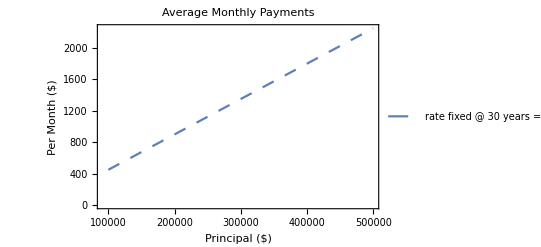

```mathematica
PlotMonthly30fixed=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"rate fixed @ 30 years = 0.0351"},Frame->True,FrameLabel->{"Principal ($)","Per Month ($)"},PlotLabel->HoldForm["Average Monthly Payments"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
rate=0.0295;
n=12;
t=15;
Monthly15fixed[Principal_]:=Principal*(rate/n(1+rate/n)^(n*t))/((1+rate/n)^(n *t)-1)
Qmax=500000;
Qmin=100000;
Npt=40;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
MonthlyTable15fixed=Table[{Q[i],Monthly15fixed[Q[i]]},{i,0,Npt}];
```

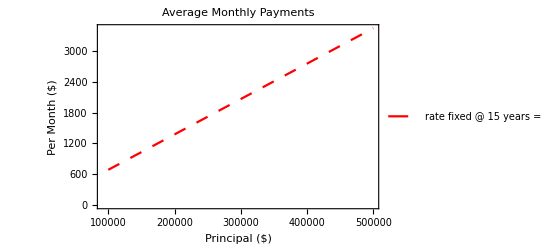

```mathematica
PlotMonthly15fixed=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium],Red},PlotLegends->{"rate fixed @ 15 years = 0.0295"},Frame->True,FrameLabel->{"Principal ($)","Per Month ($)"},PlotLabel->HoldForm["Average Monthly Payments"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

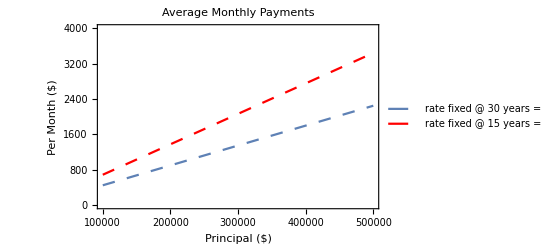

```mathematica
Show[PlotMonthly30fixed,PlotMonthly15fixed,PlotRange->{{100000,500000},{0,4000}}]
```

```mathematica
MonthlyTable30fixed
MonthlyTable15fixed
```

(100000 | 449.603
110000 | 494.563
120000 | 539.524
130000 | 584.484
140000 | 629.444
150000 | 674.405
160000 | 719.365
170000 | 764.325
180000 | 809.286
190000 | 854.246
200000 | 899.206
210000 | 944.166
220000 | 989.127
230000 | 1034.09
240000 | 1079.05
250000 | 1124.01
260000 | 1168.97
270000 | 1213.93
280000 | 1258.89
290000 | 1303.85
300000 | 1348.81
310000 | 1393.77
320000 | 1438.73
330000 | 1483.69
340000 | 1528.65
350000 | 1573.61
360000 | 1618.57
370000 | 1663.53
380000 | 1708.49
390000 | 1753.45
400000 | 1798.41
410000 | 1843.37
420000 | 1888.33
430000 | 1933.29
440000 | 1978.25
450000 | 2023.21
460000 | 2068.17
470000 | 2113.13
480000 | 2158.09
490000 | 2203.06
500000 | 2248.02)

(100000 | 688.179
110000 | 756.997
120000 | 825.815
130000 | 894.633
140000 | 963.451
150000 | 1032.27
160000 | 1101.09
170000 | 1169.91
180000 | 1238.72
190000 | 1307.54
200000 | 1376.36
210000 | 1445.18
220000 | 1513.99
230000 | 1582.81
240000 | 1651.63
250000 | 1720.45
260000 | 1789.27
270000 | 1858.08
280000 | 1926.9
290000 | 1995.72
300000 | 2064.54
310000 | 2133.36
320000 | 2202.17
330000 | 2270.99
340000 | 2339.81
350000 | 2408.63
360000 | 2477.45
370000 | 2546.26
380000 | 2615.08
390000 | 2683.9
400000 | 2752.72
410000 | 2821.54
420000 | 2890.35
430000 | 2959.17
440000 | 3027.99
450000 | 3096.81
460000 | 3165.63
470000 | 3234.44
480000 | 3303.26
490000 | 3372.08
500000 | 3440.9)

## Fixed Interest Total Accrual

```mathematica
rate=0.0351;
n=12;
t=30;
Accrual30fixed[Principal_]:=Principal*(n*t)(rate/n(1+rate/n)^(n*t))/((1+rate/n)^(n *t)-1)
Qmax=500000;
Qmin=100000;
Npt=40;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualTable30fixed=Table[{Q[i],Accrual30fixed[Q[i]]},{i,0,Npt}];
```

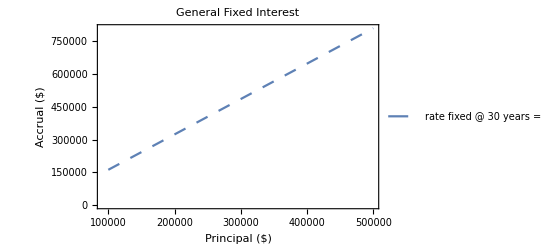

```mathematica
PlotAccrual30fixed=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"rate fixed @ 30 years = 0.0351"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Fixed Interest"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

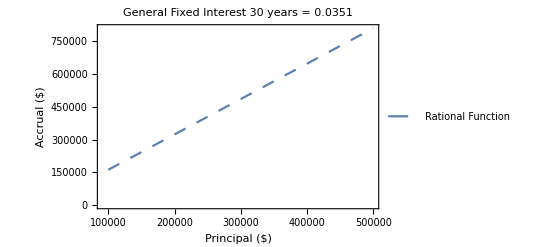

```mathematica
PlotAccrual30fixedNT=ListPlot[%%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Rational Function"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Fixed Interest 30 years = 0.0351"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
rate=0.0295;
n=12;
t=15;
Accrual15fixed[Principal_]:=Principal*(n*t)(rate/n(1+rate/n)^(n*t))/((1+rate/n)^(n *t)-1)
Qmax=500000;
Qmin=100000;
Npt=40;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualTable15fixed=Table[{Q[i],Accrual15fixed[Q[i]]},{i,0,Npt}];
```

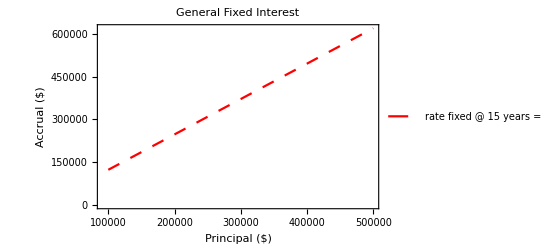

```mathematica
PlotAccrual15fixed=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium],Red},PlotLegends->{"rate fixed @ 15 years = 0.0295"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Fixed Interest"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

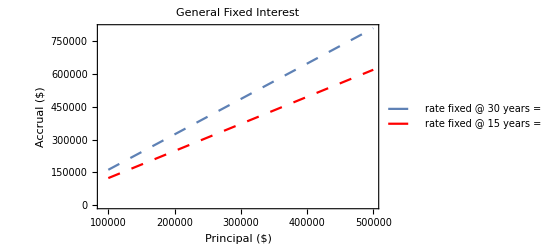

```mathematica
Show[PlotAccrual30fixed,PlotAccrual15fixed]
```

```mathematica
AccrualTable30fixed
AccrualTable15fixed
```

(100000 | 161857.
110000 | 178043.
120000 | 194229.
130000 | 210414.
140000 | 226600.
150000 | 242786.
160000 | 258971.
170000 | 275157.
180000 | 291343.
190000 | 307529.
200000 | 323714.
210000 | 339900.
220000 | 356086.
230000 | 372271.
240000 | 388457.
250000 | 404643.
260000 | 420828.
270000 | 437014.
280000 | 453200.
290000 | 469386.
300000 | 485571.
310000 | 501757.
320000 | 517943.
330000 | 534128.
340000 | 550314.
350000 | 566500.
360000 | 582686.
370000 | 598871.
380000 | 615057.
390000 | 631243.
400000 | 647428.
410000 | 663614.
420000 | 679800.
430000 | 695986.
440000 | 712171.
450000 | 728357.
460000 | 744543.
470000 | 760728.
480000 | 776914.
490000 | 793100.
500000 | 809286.)

(100000 | 123872.
110000 | 136260.
120000 | 148647.
130000 | 161034.
140000 | 173421.
150000 | 185808.
160000 | 198196.
170000 | 210583.
180000 | 222970.
190000 | 235357.
200000 | 247745.
210000 | 260132.
220000 | 272519.
230000 | 284906.
240000 | 297294.
250000 | 309681.
260000 | 322068.
270000 | 334455.
280000 | 346842.
290000 | 359230.
300000 | 371617.
310000 | 384004.
320000 | 396391.
330000 | 408779.
340000 | 421166.
350000 | 433553.
360000 | 445940.
370000 | 458328.
380000 | 470715.
390000 | 483102.
400000 | 495489.
410000 | 507876.
420000 | 520264.
430000 | 532651.
440000 | 545038.
450000 | 557425.
460000 | 569813.
470000 | 582200.
480000 | 594587.
490000 | 606974.
500000 | 619362.)

## Fixed Interest Monthly Payments, exponential

```mathematica
rate=0.0351;
n=12;
t=30;
Monthly30fixedexp[Principal_]:=Principal*(rate/n*ⅇ^(rate*t))/(ⅇ^(rate *t)-1)
Qmax=500000;
Qmin=100000;
Npt=40;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
MonthlyTable30fixedexp=Table[{Q[i],Monthly30fixedexp[Q[i]]},{i,0,Npt}];
```

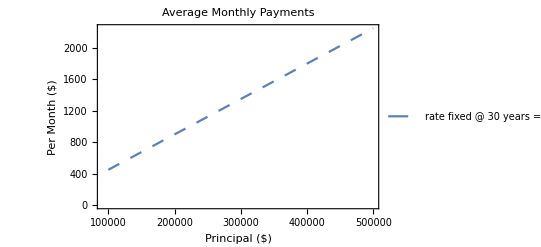

```mathematica
PlotMonthly30fixedexp=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"rate fixed @ 30 years = 0.0351"},Frame->True,FrameLabel->{"Principal ($)","Per Month ($)"},PlotLabel->HoldForm["Average Monthly Payments"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
rate=0.0295;
n=12;
t=15;
Monthly15fixedexp[Principal_]:=Principal*(rate/n*ⅇ^(rate*t))/(ⅇ^(rate *t)-1)
Qmax=500000;
Qmin=100000;
Npt=40;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
MonthlyTable15fixedexp=Table[{Q[i],Monthly15fixedexp[Q[i]]},{i,0,Npt}];
```

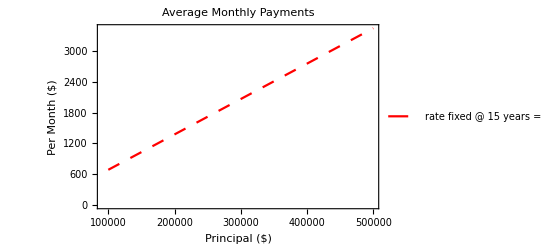

```mathematica
PlotMonthly15fixedexp=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium],Red},PlotLegends->{"rate fixed @ 15 years = 0.0295"},Frame->True,FrameLabel->{"Principal ($)","Per Month ($)"},PlotLabel->HoldForm["Average Monthly Payments"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

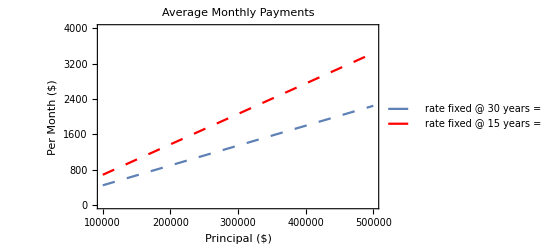

```mathematica
Show[PlotMonthly30fixedexp,PlotMonthly15fixedexp,PlotRange->{{100000,500000},{0,4000}}]
```

```mathematica
MonthlyTable30fixedexp
MonthlyTable15fixedexp
```

(100000 | 449.233
110000 | 494.156
120000 | 539.079
130000 | 584.002
140000 | 628.926
150000 | 673.849
160000 | 718.772
170000 | 763.695
180000 | 808.619
190000 | 853.542
200000 | 898.465
210000 | 943.388
220000 | 988.312
230000 | 1033.23
240000 | 1078.16
250000 | 1123.08
260000 | 1168.
270000 | 1212.93
280000 | 1257.85
290000 | 1302.77
300000 | 1347.7
310000 | 1392.62
320000 | 1437.54
330000 | 1482.47
340000 | 1527.39
350000 | 1572.31
360000 | 1617.24
370000 | 1662.16
380000 | 1707.08
390000 | 1752.01
400000 | 1796.93
410000 | 1841.85
420000 | 1886.78
430000 | 1931.7
440000 | 1976.62
450000 | 2021.55
460000 | 2066.47
470000 | 2111.39
480000 | 2156.32
490000 | 2201.24
500000 | 2246.16)

(100000 | 687.508
110000 | 756.259
120000 | 825.009
130000 | 893.76
140000 | 962.511
150000 | 1031.26
160000 | 1100.01
170000 | 1168.76
180000 | 1237.51
190000 | 1306.26
200000 | 1375.02
210000 | 1443.77
220000 | 1512.52
230000 | 1581.27
240000 | 1650.02
250000 | 1718.77
260000 | 1787.52
270000 | 1856.27
280000 | 1925.02
290000 | 1993.77
300000 | 2062.52
310000 | 2131.27
320000 | 2200.03
330000 | 2268.78
340000 | 2337.53
350000 | 2406.28
360000 | 2475.03
370000 | 2543.78
380000 | 2612.53
390000 | 2681.28
400000 | 2750.03
410000 | 2818.78
420000 | 2887.53
430000 | 2956.28
440000 | 3025.03
450000 | 3093.79
460000 | 3162.54
470000 | 3231.29
480000 | 3300.04
490000 | 3368.79
500000 | 3437.54)

## Fixed Interest Total Accrual, exponential

```mathematica
rate=0.0351;
n=12;
t=30;
Accrual30fixedexp[Principal_]:=Principal*(n*t)*(rate/n*ⅇ^(rate*t))/(ⅇ^(rate *t)-1)
Qmax=500000;
Qmin=100000;
Npt=40;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualTable30fixedexp=Table[{Q[i],Accrual30fixedexp[Q[i]]},{i,0,Npt}];
```

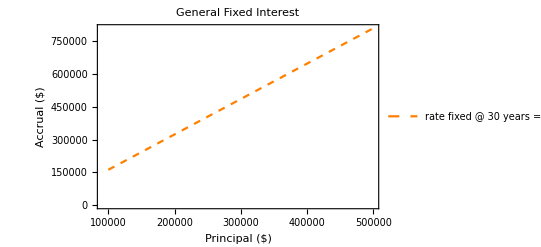

```mathematica
PlotAccrual30fixedexp=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Small],Orange},PlotLegends->{"rate fixed @ 30 years = 0.0351"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Fixed Interest"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

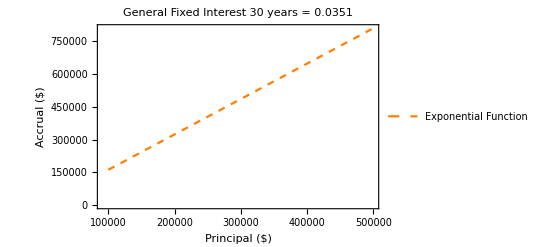

```mathematica
PlotAccrual30fixedexpNT=ListPlot[%%, Joined-> True,PlotStyle->{Dashing[Small],Orange},PlotLegends->{"Exponential Function"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Fixed Interest 30 years = 0.0351"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
rate=0.0295;
n=12;
t=15;
Accrual15fixedexp[Principal_]:=Principal*(n*t)*(rate/n*ⅇ^(rate*t))/(ⅇ^(rate *t)-1)
Qmax=500000;
Qmin=100000;
Npt=40;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualTable15fixedexp=Table[{Q[i],Accrual15fixedexp[Q[i]]},{i,0,Npt}];
```

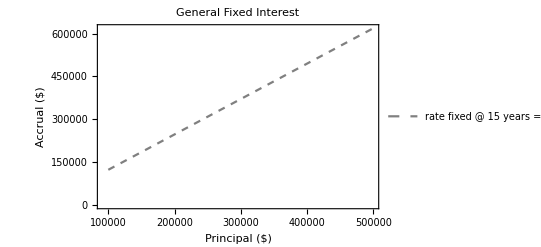

```mathematica
PlotAccrual15fixedexp=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Small],Gray},PlotLegends->{"rate fixed @ 15 years = 0.0295"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Fixed Interest"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

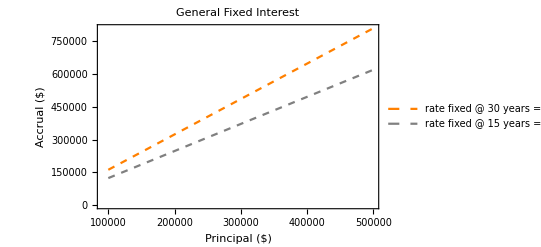

```mathematica
Show[PlotAccrual30fixedexp,PlotAccrual15fixedexp]
```

```mathematica
AccrualTable30fixedexp
AccrualTable15fixedexp
```

(100000 | 161724.
110000 | 177896.
120000 | 194068.
130000 | 210241.
140000 | 226413.
150000 | 242586.
160000 | 258758.
170000 | 274930.
180000 | 291103.
190000 | 307275.
200000 | 323447.
210000 | 339620.
220000 | 355792.
230000 | 371965.
240000 | 388137.
250000 | 404309.
260000 | 420482.
270000 | 436654.
280000 | 452826.
290000 | 468999.
300000 | 485171.
310000 | 501343.
320000 | 517516.
330000 | 533688.
340000 | 549861.
350000 | 566033.
360000 | 582205.
370000 | 598378.
380000 | 614550.
390000 | 630722.
400000 | 646895.
410000 | 663067.
420000 | 679240.
430000 | 695412.
440000 | 711584.
450000 | 727757.
460000 | 743929.
470000 | 760101.
480000 | 776274.
490000 | 792446.
500000 | 808619.)

(100000 | 123751.
110000 | 136127.
120000 | 148502.
130000 | 160877.
140000 | 173252.
150000 | 185627.
160000 | 198002.
170000 | 210377.
180000 | 222753.
190000 | 235128.
200000 | 247503.
210000 | 259878.
220000 | 272253.
230000 | 284628.
240000 | 297003.
250000 | 309379.
260000 | 321754.
270000 | 334129.
280000 | 346504.
290000 | 358879.
300000 | 371254.
310000 | 383629.
320000 | 396005.
330000 | 408380.
340000 | 420755.
350000 | 433130.
360000 | 445505.
370000 | 457880.
380000 | 470255.
390000 | 482631.
400000 | 495006.
410000 | 507381.
420000 | 519756.
430000 | 532131.
440000 | 544506.
450000 | 556881.
460000 | 569257.
470000 | 581632.
480000 | 594007.
490000 | 606382.
500000 | 618757.)

## Compare Functions

```mathematica
AccrualTable30fixed
AccrualTable30fixedexp
```

(100000 | 161857.
110000 | 178043.
120000 | 194229.
130000 | 210414.
140000 | 226600.
150000 | 242786.
160000 | 258971.
170000 | 275157.
180000 | 291343.
190000 | 307529.
200000 | 323714.
210000 | 339900.
220000 | 356086.
230000 | 372271.
240000 | 388457.
250000 | 404643.
260000 | 420828.
270000 | 437014.
280000 | 453200.
290000 | 469386.
300000 | 485571.
310000 | 501757.
320000 | 517943.
330000 | 534128.
340000 | 550314.
350000 | 566500.
360000 | 582686.
370000 | 598871.
380000 | 615057.
390000 | 631243.
400000 | 647428.
410000 | 663614.
420000 | 679800.
430000 | 695986.
440000 | 712171.
450000 | 728357.
460000 | 744543.
470000 | 760728.
480000 | 776914.
490000 | 793100.
500000 | 809286.)

(100000 | 161724.
110000 | 177896.
120000 | 194068.
130000 | 210241.
140000 | 226413.
150000 | 242586.
160000 | 258758.
170000 | 274930.
180000 | 291103.
190000 | 307275.
200000 | 323447.
210000 | 339620.
220000 | 355792.
230000 | 371965.
240000 | 388137.
250000 | 404309.
260000 | 420482.
270000 | 436654.
280000 | 452826.
290000 | 468999.
300000 | 485171.
310000 | 501343.
320000 | 517516.
330000 | 533688.
340000 | 549861.
350000 | 566033.
360000 | 582205.
370000 | 598378.
380000 | 614550.
390000 | 630722.
400000 | 646895.
410000 | 663067.
420000 | 679240.
430000 | 695412.
440000 | 711584.
450000 | 727757.
460000 | 743929.
470000 | 760101.
480000 | 776274.
490000 | 792446.
500000 | 808619.)

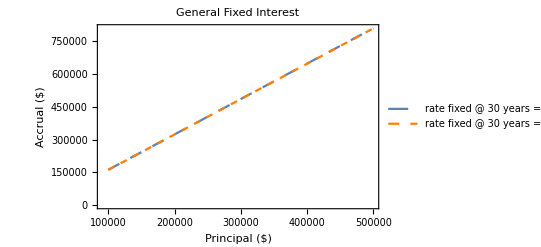

```mathematica
Show[PlotAccrual30fixed,PlotAccrual30fixedexp]
```

```mathematica
Accrual30fixed[400000]-Accrual30fixedexp[400000]
```

483.534

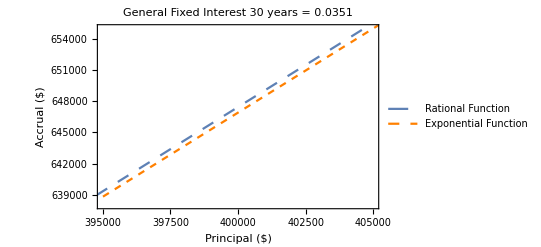

```mathematica
Show[PlotAccrual30fixedNT,PlotAccrual30fixedexpNT,PlotRange->{{395000,405000},{638000,655000}}]
```

```mathematica
Accrual15fixed[400000]-Accrual15fixedexp[400000]
```

483.534